# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(* duration for moving operations: Split,Combine, and physical swap*)
DurMove-><|"Alice"->4, "Bob"->5|>,

(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,

(* Readout: fidelity. It has bitflip error 
Scattering error affecting the neighborhood qubits, e.g., collaps the superposition into 0
*)
FidRead-><|"Alice"->0.98, "Bob"->0.99|>,
DurRead-><|"Alice"->20, "Bob"->20|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone
 *)
FidSingleXY-><|"Alice"->0.9999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{1,0},"Bob"->{0.9,0.1}|>,

(* rabi frequency on single rotations in MHz *)
RabiFreq-><|"Alice"->5, "Bob"->5 |>,

(* frequency of CZ operation*)
FreqCZ-><|"Alice"->5*10^3,"Bob"->3.3*10^3|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>,
(* frequency of remote entanglement *)
FreqEnt->6*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.8,
EFEnt->{1,0}
};
```

All nodes are simulated in one big density matrix that is paritioned.

T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
modifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.

Questlink takes initial indices; thus, passive noise is incorrect. Thus, passive noise is manually added for every gate.
Passive noise different on each zone.

Spatial move operations (SplitZ, CombS, PSwap) and quantum operations (the rest) must be done separately to follow the correct zone rules.
CombS, combine string within the zone not yet applied completely? (do one needs to combine string before applying 2-qubit gates?). Can one accidentally perform combine multiple times?  The noise on the move operations? (passive noise)

Correlated noise happens only to qubits with the same zone.

Should SplitZ_(p,q)=SplitZ_(q,p)? (no, split is correct)

ToZone_q operation? see p. 19→20 (shuttle_q____)

The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.

Exact operations on entangling (forget everything before, then assign it to 01+10

Parrallel -> None, Default (no operations in the same zone, always parallel Alice and Bob) , Full (Default+ parallel when in different zone)

native gates :  Init, Read, Rx, Ry, CZ, Ent[node1, node2], SWAP, SplitZ, CombS  

Zone1 : prepare, store?, detect
Zone2 : prepare, store?, detect, logic
Zone3 : prepare, store?, detect, logic
Zone4 : remote entangle

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
ncirc=InsertCircuitNoise[{Subscript[SplitZ, 2,3]["Alice",3],Subscript[SplitZ, 2,3]["Bob",3]},dev,ReplaceAliases->False];
DrawCircuit@ncirc;
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev@NumAccessibleQubits
```

8

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ=CreateQureg[8];
```

```mathematica
circ={Subscript[SplitZ, 2,3]["Alice",3],Subscript[SplitZ, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[SplitZ, 3,4]["Alice",4],Subscript[SplitZ, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[CombS, 3,4]["Alice",3],Subscript[CombS, 3,4]["Bob",3],Subscript[SWAP, 3,4]["Alice"],Subscript[SWAP, 3,4]["Bob"],Subscript[SplitZ, 4,3]["Alice",4],Subscript[SplitZ, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[CombS, 4,3]["Alice",3],Subscript[CombS, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[SplitZ, 4,3]["Alice",2],Subscript[SplitZ, 4,3]["Bob",2],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[SplitZ, 1,2]["Alice",2],Subscript[SplitZ, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[CombS, 2,4]["Alice"]};
```

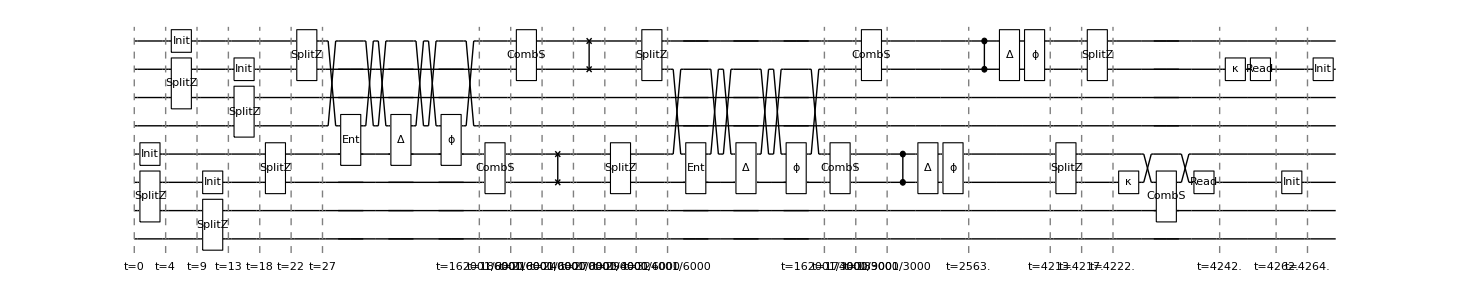

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
ncirc=InsertCircuitNoise[circ,dev,ReplaceAliases->False];
DrawCircuit@ncirc
dev@ShowNodes
```

```mathematica
Subscript[Split, 4,2]["Bob",3]
```

```mathematica
SetQuregMatrix[ρ,RandomMixState[8]];
```

```mathematica
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[circ,TrappedIonOxford[],ReplaceAliases->True]]
```

{{0},{1}}

```mathematica
nodes=Keys@OptionValue[TrappedIonOxford,Nodes]
```

{Alice,Bob}

```mathematica
(*separate circ *)
qmap=<|"Alice"-><|1->0,2->1,3->2,4->3|>,"Bob"-><|1->4,2->5,3->6,4->7|>|>;
```

```mathematica
circ
```

{SplitZ_(2,3)[Alice,3],SplitZ_(2,3)[Bob,3],Init_3[Alice],Init_4[Alice],Init_3[Bob],Init_4[Bob],SplitZ_(3,4)[Alice,4],SplitZ_(3,4)[Bob,4],Ent_(4,4)[Alice,Bob],CombS_(3,4)[Alice,3],CombS_(3,4)[Bob,3],SWAP_(3,4)[Alice],SWAP_(3,4)[Bob],SplitZ_(4,3)[Alice,4],SplitZ_(4,3)[Bob,4],Ent_(3,3)[Alice,Bob],CombS_(4,3)[Alice,3],CombS_(4,3)[Bob,3],CZ_(4,3)[Alice],CZ_(4,3)[Bob],SplitZ_(4,3)[Alice,2],SplitZ_(4,3)[Bob,2],Read_3[Alice],Read_3[Bob],SplitZ_(1,2)[Alice,2],SplitZ_(1,2)[Bob,2],Init_3[Alice],Init_3[Bob],CombS_(2,4)[Alice]}

```mathematica
circ/.{
Subscript[Ent, p_,q_][n1_,n2_]:>Subscript[Ent, qmap[n1][p],qmap[n2][q]][n1,n2],
Subscript[g_, p_,q_][n_,z_Integer]:>Subscript[g, qmap[n][p],qmap[n][q]][n,z],
Subscript[g_, q_][n_]:>Subscript[g, qmap[n][q]][n],
Subscript[g_, p_,q_][n_]:>Subscript[g, qmap[n][p],qmap[n][q]][n]
}
```

{SplitZ_(1,2)[Alice,3],SplitZ_(5,6)[Bob,3],Init_2[Alice],Init_3[Alice],Init_6[Bob],Init_7[Bob],SplitZ_(2,3)[Alice,4],SplitZ_(6,7)[Bob,4],Ent_(3,7)[Alice,Bob],CombS_(2,3)[Alice,3],CombS_(6,7)[Bob,3],SWAP_(2,3)[Alice],SWAP_(6,7)[Bob],SplitZ_(3,2)[Alice,4],SplitZ_(7,6)[Bob,4],Ent_(2,6)[Alice,Bob],CombS_(3,2)[Alice,3],CombS_(7,6)[Bob,3],CZ_(3,2)[Alice],CZ_(7,6)[Bob],SplitZ_(3,2)[Alice,2],SplitZ_(7,6)[Bob,2],Read_2[Alice],Read_6[Bob],SplitZ_(0,1)[Alice,2],SplitZ_(4,5)[Bob,2],Init_2[Alice],Init_6[Bob],CombS_(1,3)[Alice]}

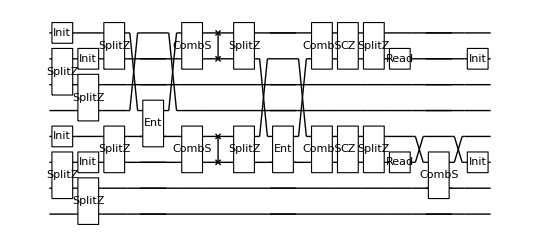

```mathematica
DrawCircuit@%
```